# octet.experiment.data.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.experiment.data.nb

this nb is to record the octet ge gm experiment data.

## initial

```mathematica
Needs["ErrorBarPlots`"]
```

## nucleon`ge`strange

```mathematica
data`nucleon`ge`s={
{{0,0},ErrorBar[0]},
{{0.05,0.001124702644},ErrorBar[0.00042369]},
{{0.1,0.001707193768},ErrorBar[0.000616653]},
{{0.15,0.002246189851},ErrorBar[0.000778041]},
{{0.2,0.002231676992},ErrorBar[0.000833645]},
{{0.25,0.002445556207},ErrorBar[0.000945724]},
{{0.3,0.002659845718},ErrorBar[0.00104725]},
{{0.35,0.002726435358},ErrorBar[0.00112127]},
{{0.4,0.002756239279},ErrorBar[0.00114272]},
{{0.45,0.003696516179},ErrorBar[0.00132153]},
{{0.5,0.003632884057},ErrorBar[0.00138048]}};
```

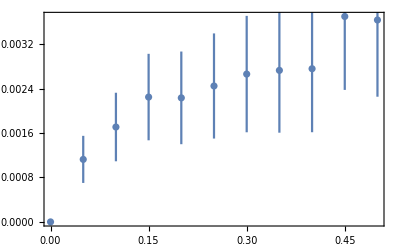

```mathematica
fig`exp`nucleon`ge`s=ErrorListPlot[
data`nucleon`ge`s,
(*figure configurations*)
AxesOrigin->{0,0},
PlotRange->{Full,Full},
PlotRangePadding->{Automatic,Scaled[.3]},
ImageSize->Scaled[0.4],
AspectRatio->1/GoldenRatio,
Frame->True
]
```

## s in proton

-Graphics-Nucleon.Ge.s

## nucleon`gm`strange

```mathematica
data`nucleon`gm`s={
{{0,-0.06423700498},ErrorBar[0.0168356]},
{{0.05,-0.04284891793},ErrorBar[0.0102095]},
{{0.1,-0.03743683104},ErrorBar[0.0114205]},
{{0.15,-0.02424724195},ErrorBar[0.00621208]},
{{0.2,-0.01849545279},ErrorBar[0.00479972]},
{{0.25,-0.01771258857},ErrorBar[0.00435548]},
{{0.3,-0.01543411254},ErrorBar[0.00428035]},
{{0.35,-0.01239120693},ErrorBar[0.00505773]},
{{0.4,-0.0107490449},ErrorBar[0.00535843]},
{{0.45,-0.01032118392},ErrorBar[0.00614265]},
{{0.5,-0.007114672445},ErrorBar[0.00564711]}
};
```

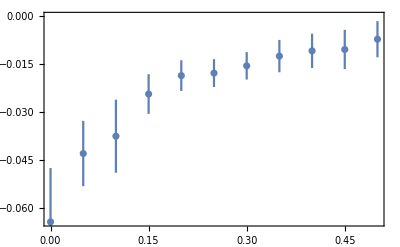

```mathematica
fig`exp`nucleon`gm`s=ErrorListPlot[
data`nucleon`gm`s,
(*figure configurations*)
AxesOrigin->{0,0},
PlotRange->{Full,Full},
PlotRangePadding->{Automatic,Scaled[.3]},
ImageSize->Scaled[0.4],
AspectRatio->1/GoldenRatio,
Frame->True
]
```